Множество дуг покрывающего дерева

{2->5,2->1,1->3,7->3,4->7,3->6}

Множество дуг, которые не вошли в покрывающее дерево

{1->7,3->4,5->1,5->3,5->4,6->5,7->5}

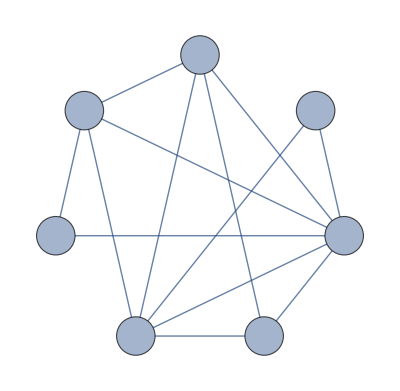

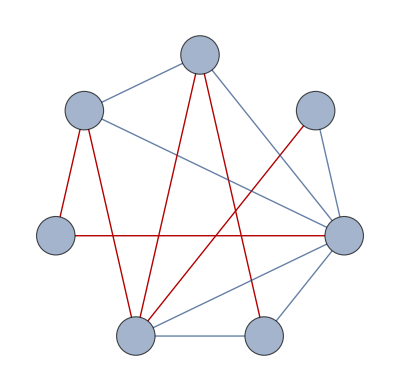

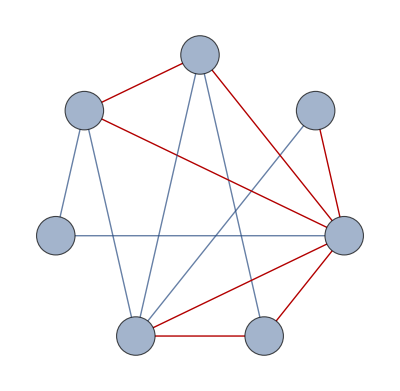

Покрывающее дерево

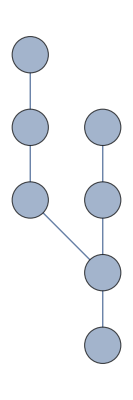

Корневое дерево с подсвеченным корнем

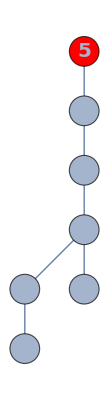

Root = 5

vertex | 1 | 2 | 3 | 4 | 5 | 6 | 7
pred | 2 | 5 | 1 | 7 | 0 | 3 | 3
dir | 1 | -1 | 1 | -1 | 0 | 1 | -1
depth | 2 | 1 | 3 | 5 | 0 | 4 | 4
d | 5 | 2 | 1 | 3 | 7 | 4 | 6

```mathematica
inFileName=StringJoin[{NotebookDirectory[],"input.txt"}];
fileStream=OpenRead[inFileName];
vertex=Read[fileStream, {Word,Number}][[2]];
edge=Read[fileStream, {Word,Number}][[2]];
edges=ReadList[fileStream,Expression,edge];
vertexList=Array[#&,vertex];
edgesList=Table[edges[[i,1]]->edges[[i,2]],{i,edge}];
graph=Graph[vertexList,edgesList,{ GraphLayout->"CircularEmbedding", VertexSize->0.3, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Bold,Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]}];


pred=ConstantArray[0,vertex];
depth=ConstantArray[0,vertex];
dir=ConstantArray[0,vertex];
listUt={};
dinast={};

dinastVertex={};
prev=root;
BuildSpanningTreeForGraph[g_,root_]:=Module[{s={}},
DepthFirstScan[UndirectedGraph[g],root,{"FrontierEdge"->Function[e,{AppendTo[s,e[[1]]->e[[2]]],pred[[e[[2]]]]=e[[1]],depth[[e[[2]]]]=1+depth[[e[[1]]]]}],"PrevisitVertex"->Function[u,AppendTo[dinastVertex,u]]}];
For[k=1,k≤Length[s],k++,arc=s[[k]];
If[MemberQ[edgesList,arc],{dir[[arc[[2]]]]=1;AppendTo[listUt,arc]},{dir[[arc[[2]]]]=-1;AppendTo[listUt,Reverse[arc]]}];];
Return[s];];



root=5;
(*1,3*)
DFS=BuildSpanningTreeForGraph[graph,root];
(*2*)
Print["Множество дуг покрывающего дерева"]
listUt
Print["Множество дуг, которые не вошли в покрывающее дерево"]
listUn=Complement[edgesList,listUt] (*Un=U\Ut*)
(*4*)
graph
HighlightGraph[graph,listUt,VertexLabels->"Some"]
HighlightGraph[graph,listUn,VertexLabels->"Some"]
Print["Покрывающее дерево"]
Graph[listUt,GraphLayout->{ "LayeredDigraphEmbedding","RootVertex"->root},VertexSize->0.5, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Bold,Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.12]]
Print["Корневое дерево с подсвеченным корнем"]
TreeGraph[DFS,GraphLayout->{ "LayeredDigraphEmbedding","RootVertex"->root},VertexSize->0.5, VertexLabels->Placed["Name", Center],VertexStyle->{root->Red}, VertexLabelStyle->Directive[Bold,Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.12]]
all={Prepend[vertexList,"vertex"],Prepend[pred,"pred"],Prepend[dir,"dir"],Prepend[depth,"depth"],Prepend[dinastVertex,"d"]};
Print["Root = ",root]
Text[Grid[all,Alignment->Left,Spacings->{2,1},Frame->All]]
```